```mathematica
(*1. Nullcline with VectorPlot*)
```

```mathematica
parameter={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->.8,λp->1,dp->1,n->2,k->10};
```

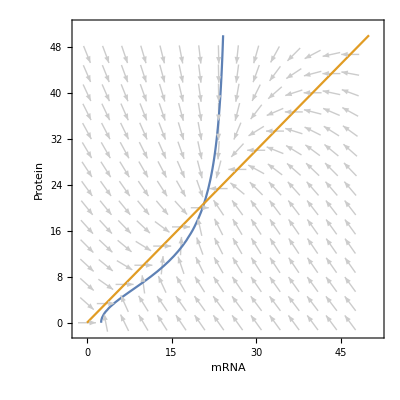

```mathematica
f[m_,p_]=Subscript[λ, m1]+Subscript[λ, m2]*p^n/(k^n+p^n)-dm*m/.parameter;
g[m_,p_]=λp*m-dp*p/.parameter;
vp=VectorPlot[{f[m,p],g[m,p]},{m,0,50},{p,0,50},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{m,p},VectorPoints->16,VectorStyle->{GrayLevel[0.8]},AspectRatio->1];
cp=ContourPlot[{f[m,p]==0,g[m,p]==0},{m,0,50},{p,0,50},FrameLabel->{"mRNA","Protein"},AspectRatio->1];
ptRules=NSolve[{f[m,p]==0,g[m,p]==0},{m,p}];
Show[vp,cp,FrameLabel->{"mRNA","Protein"}]
```

```mathematica
fixedpt=dm*dp+λp*Subscript[λ, m2]*n*p^(n-1)/(k^n+p^n)*(p^n/(k^n+p^n)-1)/.parameter
```

0.8+(36 p (-1+p^2/(100+p^2)))/(100+p^2)

```mathematica
ptRules=NSolve[{f[m,p]==0,g[m,p]==0},{m,p}]
```

{{m→20.7638,p→20.7638},{m→2.11811-2.74842 ⅈ,p→2.11811-2.74842 ⅈ},{m→2.11811+2.74842 ⅈ,p→2.11811+2.74842 ⅈ}}

```mathematica
pt=fixedpt/.p->16.513878188659973
```

0.37203

```mathematica
(*Some ideas: 1. Hill number / 2. K value(certain range) / 3. Slope of linear line λp,dp*)
```

```mathematica
(*Different hill numbers*)
```

```mathematica
Manipulate[hillnumparameter={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->.8,λp->1,dp->1,n->hillnum,k->10};f[m_,p_]=Subscript[λ, m1]+Subscript[λ, m2]*p^n/(k^n+p^n)-dm*m/.hillnumparameter;
g[m_,p_]=λp*m-dp*p/.hillnumparameter;ContourPlot[{f[m,p]==0,g[m,p]==0},{m,0,50},{p,0,50},FrameLabel->{"mRNA","Protein"},AspectRatio->1],{{hillnum,1},1,10}]
```

```mathematica
(*Focus on Hill number 4, multiple stable steady states*)
```

```mathematica
hillnum4parameter={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->0.8,λp->1,dp->1,n->4,k->10};
```

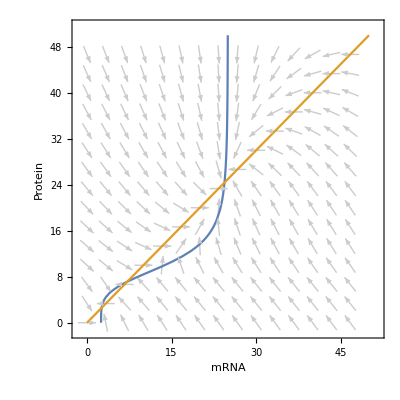

```mathematica
f[m_,p_]=Subscript[λ, m1]+Subscript[λ, m2]*p^n/(k^n+p^n)-dm*m/.hillnum4parameter;
g[m_,p_]=λp*m-dp*p/.hillnum4parameter;
vp=VectorPlot[{f[m,p],g[m,p]},{m,0,50},{p,0,50},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{m,p},VectorPoints->16,VectorStyle->{GrayLevel[0.8]},AspectRatio->1];
cp=ContourPlot[{f[m,p]==0,g[m,p]==0},{m,0,50},{p,0,50},FrameLabel->{"mRNA","Protein"},AspectRatio->1];
ptRules=NSolve[{f[m,p]==0,g[m,p]==0},{m,p}];
Show[vp,cp,FrameLabel->{"mRNA","Protein"}]
```

```mathematica
det=dm*dp+λp*Subscript[λ, m2]*n*p^(n-1)/(k^n+p^n)*(p^n/(k^n+p^n)-1)/.hillnum4parameter
```

0.8+(72 p^3 (-1+p^4/(10000+p^4)))/(10000+p^4)

```mathematica
ptRules=NSolve[{f[m,p]==0,g[m,p]==0},{m,p}]
```

{{m→24.3807,p→24.3807},{m→-4.56114-5.86365 ⅈ,p→-4.56114-5.86365 ⅈ},{m→-4.56114+5.86365 ⅈ,p→-4.56114+5.86365 ⅈ},{m→7.13875,p→7.13875},{m→2.60279,p→2.60279}}

```mathematica
pt1=det/.p->2.5229776601906235
```

0.685301

```mathematica
pt2=det/.p->7.966903602921646
```

-1.04999

```mathematica
pt3=det/.p->24.760825046251398
```

0.726599

```mathematica
(*K value*)
```

```mathematica
Manipulate[kvalparameter={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->.8,λp->1,dp->1,n->2,k->kval};f[m_,p_]=Subscript[λ, m1]+Subscript[λ, m2]*p^n/(k^n+p^n)-dm*m/.kvalparameter;
g[m_,p_]=λp*m-dp*p/.kvalparameter;ContourPlot[{f[m,p]==0,g[m,p]==0},{m,0,50},{p,0,50},FrameLabel->{"mRNA","Protein"},AspectRatio->1],{{kval,10},0,15}]
```

```mathematica
kvalparameter2={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->.8,λp->1,dp->1,n->2};
```

```mathematica
k=p*(Subscript[λ, m2]/(dm*dp/λp*p-Subscript[λ, m1])-1)^(1/n)
```

p (-1+λ_m2/((dm dp p)/λp-λ_m1))^(1/n)

```mathematica
kwithpar=k/.kvalparameter2
```

√(-1+18/(-2+0.8 p)) p

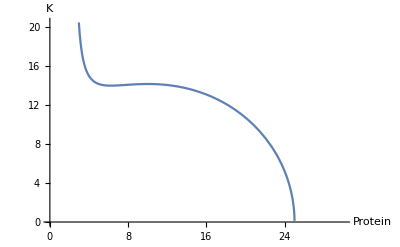

```mathematica
Plot[kwithpar,{p,0,30},AxesLabel->{Protein,K}]
```

```mathematica
D[k,p]
```

-(dm dp p λ_m2 (-1+λ_m2/((dm dp p)/λp-λ_m1))^(-1+1/n))/(n λp ((dm dp p)/λp-λ_m1)^2)+(-1+λ_m2/((dm dp p)/λp-λ_m1))^(1/n)

```mathematica
dkdp=D[k,p]/.kvalparameter2
```

√(-1+18/(-2+0.8 p))-(7.2 p)/(√(-1+18/(-2+0.8 p)) (-2+0.8 p)^2)

```mathematica
Solve[dkdp==0,p]
```

{{p→6.25},{p→10.}}

```mathematica
(*λp,dp values*)
```

```mathematica
Manipulate[rateparameter={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->.8,λp->lamdapval,dp->dpval,n->2,k->10};f[m_,p_]=Subscript[λ, m1]+Subscript[λ, m2]*p^n/(k^n+p^n)-dm*m/.rateparameter;
g[m_,p_]=λp*m-dp*p/.rateparameter;ContourPlot[{f[m,p]==0,g[m,p]==0},{m,0,50},{p,0,50},FrameLabel->{"mRNA","Protein"},AspectRatio->1],{{lamdapval,1},0.1,10},{{dpval,1},0.1,10}]
```

```mathematica
(*Timecourse graph*)
```

```mathematica
parameter={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->.8,λp->1,dp->1,n->2,k->10};
```

```mathematica
system={
m'[t]==Subscript[λ, m1]+Subscript[λ, m2]*p[t]^n/(k^n+p[t]^n)-dm*m[t],
p'[t]==λp*m[t]-dp*p[t]};
```

```mathematica
init={m[0]==5,p[0]==1};
```

```mathematica
fullsystem=Join[system,init];
```

```mathematica
numericsoln=NDSolve[fullsystem/.parameter,{m[t],p[t]},{t,0,30}]
```

{{m[t]→InterpolatingFunction[…][t],p[t]→InterpolatingFunction[…][t]}}

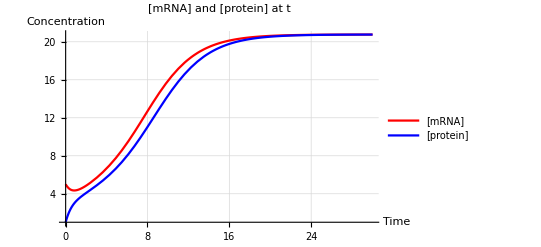

```mathematica
Plot[{{m[t]/.numericsoln},{p[t]/.numericsoln}},{t,0,30},PlotStyle->{{Red,Thick},{Blue, Thick}}, GridLines->Automatic,PlotRange->All, PlotLegends->{"[mRNA]","[protein]"},AxesLabel->{"Time","Concentration"},PlotLabel->"[mRNA] and [protein] at t"]
```

```mathematica
Manipulate[
parameter={Subscript[λ, m1]->m1val,Subscript[λ, m2]->m2val,dm->dmval,λp->lampval,dp->dpval,n->nval,k->kval};
system={
m'[t]==Subscript[λ, m1]+Subscript[λ, m2]*p[t]^n/(k^n+p[t]^n)-dm*m[t],
p'[t]==λp*m[t]-dp*p[t]};
init={m[0]==5,p[0]==1};
fullsystem=Join[system,init];
numericsoln=NDSolve[fullsystem/.parameter,{m[t],p[t]},{t,0,30}];
Plot[{{m[t]/.numericsoln},{p[t]/.numericsoln}},{t,0,30},PlotStyle->{{Red,Thick},{Blue, Thick}}, GridLines->Automatic,PlotRange->All, PlotLegends->{"[mRNA]","[protein]"},AxesLabel->{"Time","Concentration"},PlotLabel->"[mRNA] and [protein] at t"],{{m1val,2},.1,10},{{m2val,18},1,30},{{dmval,0.8},.1,10},{{lampval,1},.1,10},{{dpval,1},.1,10},{{nval,2},.1,10},{{kval,10},1,100}]
```